Solution to general 4 state model with forward k rates and reverse r rates

```mathematica
ass={ koff>0 , km>0, kp>0, kon>0, koff0<koff1, konp < kon,koff0>0, koff1>0, b > 1};
```

```mathematica
sys={k1 p1 - r1 p2, k2 p2 - r2 p3, k3 p3 - r3 p4, k4 p4 - r4 p1, p1+p2+p3+p4}
```

{k1 p1-p2 r1,k2 p2-p3 r2,k3 p3-p4 r3,k4 p4-p1 r4,p1+p2+p3+p4}

```mathematica
sys = sys/.{k1-> kon, r1-> koff, k3-> koff, r3-> konp, k2->  b kp, r2-> kmp, k4-> km, r4->  kp};
sys = sys /. {km-> 1,kmp->kon/konp} (* nondim to km *)
```

{kon p1-koff p2,b kp p2-(kon p3)/konp,koff p3-konp p4,-kp p1+p4,p1+p2+p3+p4}

```mathematica
sol = FullSimplify[Solve[{J,J,J,J,1}==sys, {J, p1,p2,p3,p4}]]
```

{{J→((-1+b) koff kon konp kp)/(koff^2 konp (1+kp)+koff konp kp (b+konp+b kp)+(kon+kon konp+konp kp) (kon+b konp kp)+koff kon (1+kp+konp (2+b kp))),p1→(koff (kon+koff konp+kon konp+b konp kp))/(koff^2 konp (1+kp)+koff konp kp (b+konp+b kp)+(kon+kon konp+konp kp) (kon+b konp kp)+koff kon (1+kp+konp (2+b kp))),p2→(kon (kon (1+konp)+konp (koff+kp)))/(koff^2 konp (1+kp)+koff konp kp (b+konp+b kp)+(kon+kon konp+konp kp) (kon+b konp kp)+koff kon (1+kp+konp (2+b kp))),p3→(konp kp (koff konp+b (kon+kon konp+konp kp)))/(koff^2 konp (1+kp)+koff konp kp (b+konp+b kp)+(kon+kon konp+konp kp) (kon+b konp kp)+koff kon (1+kp+konp (2+b kp))),p4→(koff kp (kon+b kon konp+konp (koff+b kp)))/(koff^2 konp (1+kp)+koff konp kp (b+konp+b kp)+(kon+kon konp+konp kp) (kon+b konp kp)+koff kon (1+kp+konp (2+b kp)))}}

```mathematica
check = J /.sol [[1]] /.b->1
```

0

We are treating state 3 as the productive state - i.e. the one in which transcription happens.

```mathematica
p3cb[koff_] = p3/. sol[[1]]
```

(konp kp (koff konp+b (kon+kon konp+konp kp)))/(koff^2 konp (1+kp)+koff konp kp (b+konp+b kp)+(kon+kon konp+konp kp) (kon+b konp kp)+koff kon (1+kp+konp (2+b kp)))

```mathematica
p3c[koff_] = FullSimplify[p3cb[koff] /. {b -> 1}]
```

(konp kp)/(koff+kon+(koff+konp) kp)

```mathematica
p3cb[c*koff]
```

(konp kp (c koff konp+b (kon+kon konp+konp kp)))/(c^2 koff^2 konp (1+kp)+c koff konp kp (b+konp+b kp)+(kon+kon konp+konp kp) (kon+b konp kp)+c koff kon (1+kp+konp (2+b kp)))

#### Calculate fidelity ratios in/out of equilibrium

```mathematica
eqRatio = FullSimplify[p3c[koff] / p3c[c*koff]]
noneqRatio = FullSimplify[p3cb[koff] / p3cb[c*koff]]
```

(kon+konp kp+c koff (1+kp))/(koff+kon+(koff+konp) kp)

((koff konp+b (kon+kon konp+konp kp)) (c^2 koff^2 konp (1+kp)+(kon+kon konp+konp kp) (kon+b konp kp)+c koff (konp kp (b+konp+b kp)+kon (1+2 konp+kp+b konp kp))))/((c koff konp+b (kon+kon konp+konp kp)) (koff^2 konp (1+kp)+koff konp kp (b+konp+b kp)+(kon+kon konp+konp kp) (kon+b konp kp)+koff kon (1+kp+konp (2+b kp))))

### Explore limiting behaviors at equilibrium

```mathematica
Limit[eqRatio,{koff->Infinity,kp->0}]
```

c

```mathematica
concRatio= eqRatio
```

(kon+konp kp+c koff (1+kp))/(koff+kon+(koff+konp) kp)

```mathematica
errorRate[koff_,kp_] = .5*( p3c[koff]*(1/concRatio - 1) + 1) /. {kon->1,konp->1,c->10}
```

0.5 (1+(kp (-1+(1+koff+(1+koff) kp)/(1+kp+10 koff (1+kp))))/(1+koff+(1+koff) kp))

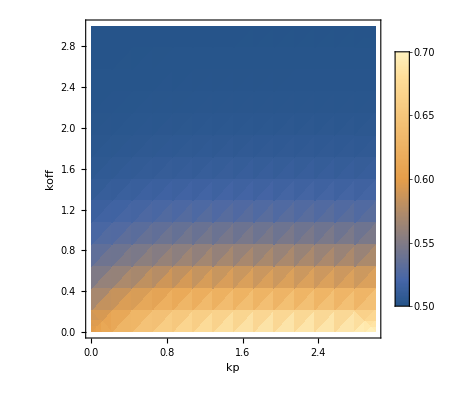

```mathematica
DensityPlot[1-errorRate[koff,kp],{kp,1,10^3},{koff,1,10^3},FrameLabel->{"kp","koff"},PlotLegends->Automatic, ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
concFunction[koff_,kp_] = concRatio /10 /. {kon->1,konp->1,c->10}
```

(1+kp+10 koff (1+kp))/(10 (1+koff+(1+koff) kp))

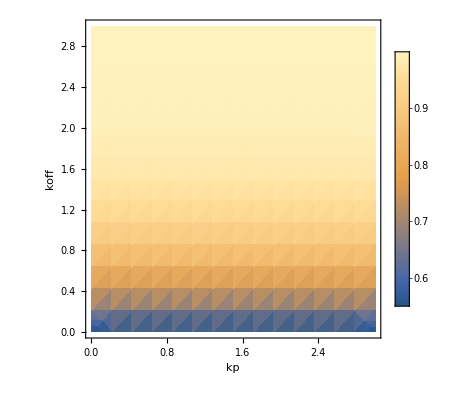

```mathematica
DensityPlot[concFunction[koff,kp],{kp,1,10^3},{koff,1,10^3},FrameLabel->{"kp","koff"},PlotLegends->Automatic, ScalingFunctions->{"Log10","Log10"}]
```